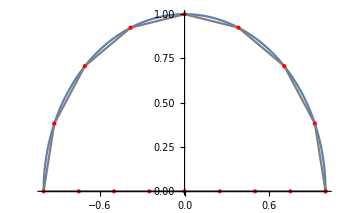

```mathematica
DivisionPointsP= {};
For [i = 0,i ≤ 8,i++,
DivisionPointsP = Insert[DivisionPointsP,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/8 π}],10],-1]
]
DivisionPointsP = Join[DivisionPointsP, {{-0.75,0 },{-0.5,0},{-0.25,0},{0,0},{0.25,0},{0.5,0},{0.75,0},{1,0}}];
Show[Plot[Sqrt[1-x^2],{x,-1,1}], ListLinePlot[DivisionPointsP,PlotStyle->{PointSize[Large],Gray}],ListPlot[DivisionPointsP,PlotStyle->{PointSize[Large],Red}]]
```

```mathematica
NumberDivideP= 40;
TotalNumberPointsP=3*NumberDivideP;
```

```mathematica
PointsOnLineP = {};
For[i=0,i≤ NumberDivideP-1,i++,
PointsOnLineP = Insert[PointsOnLineP,-1+(2*i)/NumberDivideP,-1]
];
PointsOnCurveP = {};
For[i=0,i≤ 2*NumberDivideP,i++,
PointsOnCurveP = Insert[PointsOnCurveP,i/(2*NumberDivideP),-1]
];
PointsXP=Join[PointsOnLineP,N[Cos[PointsOnCurveP*π]]];
PointsYP=Join[PointsOnLineP*0,N[Sin[PointsOnCurveP*π]]];
SegmentsLenP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
SegmentsLenP=Insert[SegmentsLenP,Norm[N[{PointsXP[[i+1]]-PointsXP[[i]],PointsYP[[i+1]]-PointsYP[[i]]}]],-1]
];
NormalPointsXP ={};
For[i=1,i≤ TotalNumberPointsP,i++,
NormalPointsXP = Insert[NormalPointsXP,(PointsYP[[i+1]]-PointsYP[[i]])/SegmentsLenP[[i]],-1]
];
NormalPointsYP ={};
For[i=1,i≤ TotalNumberPointsP,i++,
NormalPointsYP = Insert[NormalPointsYP,-(PointsXP[[i+1]]-PointsXP[[i]])/SegmentsLenP[[i]],-1]
];
```

```mathematica
FP=Function[{i,k,x,y},
FA=Function[kk,SegmentsLenP[[kk]]^2][k];
FB=Function[{kk,xx,yy},(-NormalPointsYP[[kk]]*(PointsXP[[kk]]-xx)+NormalPointsXP[[kk]]*(PointsYP[[kk]]-yy))*2*SegmentsLenP[[kk]]][k,x,y];
FE=Function[{kk,xx,yy},(PointsXP[[kk]]-xx)^2+(PointsYP[[kk]]-yy)^2][k,x,y];
Decision=4*FA*FE-FB^2;
If[i == 1,
Re[If[Decision==0,SegmentsLenP[[k]]/(2*π)*(Log[SegmentsLenP[[k]]]+(1+FB/(2*FA))*Log[Abs[1+FB/(2*FA)]]-FB/(2*FA)*Log[Abs[FB/(2*FA)]]-1),
SegmentsLenP[[k]]/(4*π)*(2*(Log[SegmentsLenP[[k]]]-1)-FB/(2*FA)*Log[Abs[FE/FA]]+(1+FB/(2*FA))*Log[Abs[1+(FB+FE)/FA]]+Sqrt[Decision]/FA*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]]))
]]
,Re[If[Decision ==0,0,SegmentsLenP[[k]]*((NormalPointsXP[[k]]*(PointsXP[[k]]-x)+NormalPointsYP[[k]]*(PointsYP[[k]]-y))/(π*Sqrt[Decision ]))*(ArcTan[(2*FA+FB)/Sqrt[Decision ]]-ArcTan[FB/Sqrt[Decision ]])
]]
]
];
```

```mathematica
MidPointsXP=N[Join[PointsOnLineP+1/(NumberDivideP*2),Cos[(PointsOnCurveP+1/(NumberDivideP*4))*π]]];
MidPointsYP=N[Join[PointsOnLineP*0,Sin[(PointsOnCurveP+1/(NumberDivideP*4))*π]]];
BoundsP={};
For[i=1,i≤ TotalNumberPointsP,i++,
BoundsP = Insert[BoundsP,N[If[N[MidPointsXP[[i]]^2+MidPointsYP[[i]]^2 ]== 1,1,0]],-1];
];
FactorXP= {};
For[i=1,i≤ TotalNumberPointsP,i++,
FactorXP = Insert[FactorXP,(PointsXP[[i+1]]-PointsXP[[i]])/2+PointsXP[[i]],-1];
]; 
FactorYP= {};
For[i=1,i≤ TotalNumberPointsP,i++,
FactorYP = Insert[FactorYP,(PointsYP[[i+1]]-PointsYP[[i]])/2+PointsYP[[i]],-1];
]; 
aP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsP,j++,
Temp = Insert[Temp,N[-FP[1,j,FactorXP[[i]],FactorYP[[i]]]],-1];
];
aP = Insert[aP,Temp,-1];
];
bP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
Temp = {};
For[j=1,j≤ TotalNumberPointsP,j++,
Temp = Insert[Temp,N[BoundsP[[j]]*(-FP[2,j,FactorXP[[i]],FactorYP[[i]]]+Function[{ii,jj},If[ii== jj,1,0]][i,j]/2)],-1];
];
bP = Insert[bP,Sum[Temp[[k]],{k,1,TotalNumberPointsP}],-1];
];
zP=LinearSolve[aP, bP];
BoundsUP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
BoundsUP = Insert[BoundsUP,N[BoundsP[[i]]],-1];
];
BoundsNP = {};
For[i=1,i≤ TotalNumberPointsP,i++,
BoundsNP = Insert[BoundsNP,zP[[i]],-1];
];
```

```mathematica
BEMP=Function[{x,y},Sum[BoundsUP[[i]]*FP[2,i,x,y]-BoundsNP[[i]]*FP[1,i,x,y] ,{i,1,TotalNumberPointsP}]];
```

```mathematica
Plot3D[BEMP[x,y],{x,-1,1},{y,0,Sqrt[1-x^2]}]
```

-Graphics3D-